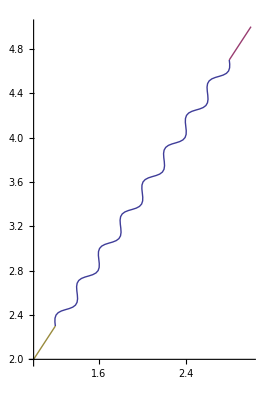

```mathematica
(* Also posted in: http://mathematica.stackexchange.com/a/37228/10 *)
ClearAll[spring]
spring::usage = "spring[ point1, point2, numberOfTurns, height, fractionToDrawAsLinesAtEnds ]" ;
spring[ a1_List, a2_List, n_Integer:8,h_:.05, f_: 0.1, p_: Automatic, e_: 0 ] :=Module[{n1, d, nd, r, r1, epilog },
If [ e == 0, epilog = {Point[{a1, a2}]}, epilog = e ] ;

n1 = Norm[a1] ;
d = a2 - a1 ;
nd = Norm[d] ;
r = RotationMatrix[ArcTan @@  d ] ;
r1 = r . {n1, 0} ;
ParametricPlot[ 
{
{a1 -r1 + r . { n1 + nd f + t (1 - 2f) nd, h Sin[ 2 Pi n t]}},
{a1 -r1 + r . { n1 + nd f + (1 - 2f) nd + t f nd, 0}},
{a1 -r1 + r . { n1 +t f nd, 0}}
}
, {t, 0, 1 }
, Epilog->epilog
, PlotRange -> p
]
]

ClearAll[springPoints]
springPoints::usage = "springPoints[ point1, point2, numberOfTurns, height, fractionToDrawAsLinesAtEnds ]" ;
springPoints[ a1_List, a2_List, n_Integer:8,h_:.05, f_: 0.1 ] :=Module[{n1, d, nd, r, r1 },

n1 = Norm[a1] ;
d = a2 - a1 ;
nd = Norm[d] ;
r = RotationMatrix[ArcTan @@  d ] ;
r1 = r . {n1, 0} ;

{
Table[ a1 -r1 + r . { n1 + nd f + t (1 - 2f) nd, h Sin[ 2 Pi n t]}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 + nd f + (1 - 2f) nd + t f nd, 0}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 +t f nd, 0}, {t, 0, 1, 0.01 } ]
}
]

ListLinePlot[springPoints[{1,2},{3,5}], AspectRatio->Automatic ]

(*spring[{1,2},{3,5}]*)
```

```mathematica
(*Style[Grid[{{200!},{MatrixPlot@IdentityMatrix@100}},ItemSize->Automatic],ImageSizeMultipliers->1]
Grid[{{200!},{MatrixPlot@IdentityMatrix@100}},ItemSize->Automatic,BaseStyle->ImageSizeMultipliers->1]
Grid[{{200!},{MatrixPlot@IdentityMatrix@100}},ItemSize->Automatic,ItemStyle->ImageSizeMultipliers->1]*)

(*Grid[{{3},{1,2}}]*)
```